```mathematica
SizedDots[n_]:= Table[ Directive[PointSize[0.05*(n+1-i)/n],Hue[i/n]],{i,n}]
```

```mathematica
Clear[k,m,g,L,Lagrange, x, θ,v,ω]
k=1.0; m=1.0; g=10.;
L=3.0;
Lagrange[x_,θ_, v_, ω_]:=0.5  m (v^2+ ((x+L)ω)^2)+ m g (x+L) Cos[θ] - 0.5 k x^2 
DxL [x_,θ_, v_, ω_]= D[Lagrange[x,θ,v,ω],x];
DθL [x_,θ_, v_, ω_]= D[Lagrange[x,θ,v,ω],θ];
DvL [x_,θ_, v_, ω_]= D[Lagrange[x,θ,v,ω],v];
DωL [x_,θ_, v_, ω_]= D[Lagrange[x,θ,v,ω],ω];
Eq1= DxL[x[t],θ[t],v[t],ω[t]] -D[  DvL[x[t],θ[t],v[t],ω[t]], t]==0
Eq2= DθL[x[t],θ[t],v[t],ω[t]] -D[  DωL[x[t],θ[t],v[t],ω[t]], t]==0
```

10. Cos[θ[t]]-1. x[t]+1. (3.+x[t]) ω[t]^2-1. v'[t]==0

-10. Sin[θ[t]] (3.+x[t])-2. (3.+x[t]) ω[t] x'[t]-1. (3.+x[t])^2 ω'[t]==0

```mathematica
{xSol,vSol,θSol,ωSol}=NDSolveValue[
{Eq1, Eq2,x'[t]==v[t], θ'[t]==ω[t], x[0]==1.2,θ[0]==5/8, v[0]==0.2, ω[0]==0.2},
{x,v,θ,ω},{t, 0, 45}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

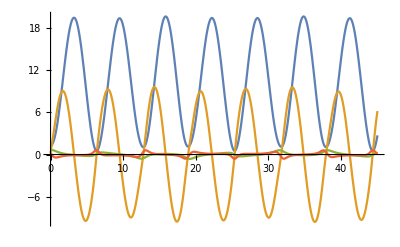

```mathematica
Plot[{xSol[t],vSol[t],θSol[t],ωSol[t]},
{t, 0, 45}]
```